```mathematica
A=({{∞, 0, 0}, {0, ∞, 0}, {0, 0, ∞}});
B={{1,2,3},{4,5,6},{7,8,9}};
A//MatrixForm
B//TableForm
```

(∞ | 0 | 0
0 | ∞ | 0
0 | 0 | ∞)

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

```mathematica
MatrixForm[A]
BB=MatrixForm[B](*Так делать НЕЛЬЗЯ, присваивать НЕЛЬЗЯ*)
```

(∞ | 0 | 0
0 | ∞ | 0
0 | 0 | ∞)

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
BB+BB
```

2 (1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
bb=Red
bb+bb
```

RGBColor[1, 0, 0]

2 RGBColor[1, 0, 0]

```mathematica
B+B//MatrixForm
```

(2 | 4 | 6
8 | 10 | 12
14 | 16 | 18)

```mathematica
Det[B]
```

0

```mathematica
A=({{a, 1, 1}, {1, a, 1}, {1, 1, a}});
X={x1,x2,x3};
Y={1,a,a^2};
Solve[A.X== Y,{x1,x2,x3}]
```

{{x1→-(1+a)/(2+a),x2→1/(2+a),x3→(1+a)^2/(2+a)}}

```mathematica
Solve[A.X== Y,{x1,x2,x3,a}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x3→1-x1-x2,a→1},{x1→(-1-a)/(2+a),x2→1/(2+a),x3→(1+a)^2/(2+a)}}

```mathematica
Reduce[A.X== Y,{x1,x2,x3}]
```

(a==1&&x3==1-x1-x2)||((-1+a) (2+a)≠0&&x1==(-1-a)/(2+a)&&x2==1+x1&&x3==1-a x1-x2)

```mathematica
Clear[x]
sol =Solve[2x^2+5x-25==0,x]
```

{{x→-5},{x→5/2}}

```mathematica
sol[[1,1,2]]
```

-5

```mathematica
sol[[2,1,1]]
```

x

```mathematica
{1,2,3,f,s,6,7,g}/.f->1000
```

{1,2,3,1000,s,6,7,g}

```mathematica
ReplaceAll[{1,2,3,f,s,6,7,g},f->1000]
```

{1,2,3,1000,s,6,7,g}

```mathematica
sol1 = x/.sol[[1]]
sol2 = x/.sol[[2]]
```

-5

5/2

```mathematica
sol1 = x/.First[sol]
sol2 = x/.sol//Last
```

-5

5/2

```mathematica
A=({{(1-a), 1, 1}, {1, (1-a), 1}, {1, 1, (1-a)}});
X={x1,x2,x3};
Y={1,(1-a),(1-a)^2};

Reduce[A.X==Y,X]
```

(a==0&&x3==1-x1-x2)||((-3+a) a≠0&&x1==(2-a)/(-3+a)&&x2==1+x1&&x3==1-x1+a x1-x2)

```mathematica
Solve[Det[A]==0,a]
```

{{a→0},{a→0},{a→3}}

```mathematica
(*Если a не равно 0 или 3*)
sol =Solve[A.X==Y,X]
a0 = 1;
x1s= x1/.sol[[1]]/.a->a0
x2s= x2/.sol[[1]]/.a->a0
x3s= x3/.sol[[1]]/.a->a0
```

{{x1→-(-2+a)/(-3+a),x2→-1/(-3+a),x3→-(-2+a)^2/(-3+a)}}

-1/2

1/2

1/2

```mathematica
(*Если a равно 0*)
sol =Solve[(A/.a->0).X==(Y/.a->0),X]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x3→1-x1-x2}}

```mathematica
x10 =10;
x20 = 1;
x30 = x3/.sol[[1]]/.{x1->x10,x2->x20}
```

-10

```mathematica
(*Если a равно 3*)
sol =Solve[(A/.a->3).X==(Y/.a->3),X]
```

{}

{{x→1/2 (-25-7 √13)},{x→1/2 (-25+7 √13)}}

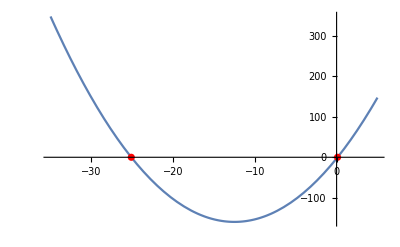

```mathematica
fun = x^2+25x-3;
sol = Solve[fun==0,x]
x01 =x/.sol[[1]];
x02 =x/.sol[[2]];
Show[
Plot[fun,{x,-35,5}],
ListPlot[{{x01,fun/.x->x01},{x02,fun/.x->x02}},PlotStyle->Red]
]
```

```mathematica
Clear["Global`*"]
fun[x_] := x^2+25x-3;
sol = Solve[fun[u]==0,u]
x01 =u/.sol[[1]];
x02 =u/.sol[[2]];
Show[
Plot[fun[x],{x,-35,5}],
ListPlot[{{x01,fun[x01]},{x02,fun[x02]}},PlotStyle->Red]
]
```

{{u→1/2 (-25-7 √13)},{u→1/2 (-25+7 √13)}}

-Graphics-

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s).

{x→0.}

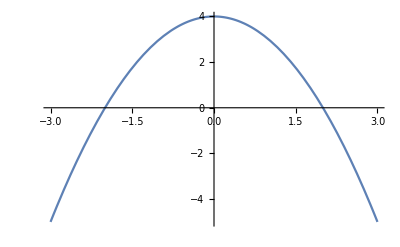

```mathematica
FindRoot[-x^2+4==0,{x,0}]
Plot[-x^2+4,{x,-3,3}]
```

```mathematica
v=1
```

1

```mathematica
v1:=1
```

```mathematica
v1
```

1

```mathematica
v2="kd";
v3="kd";
v2==v3
```

True

```mathematica
x=RandomReal[];
y:=RandomReal[];
{x,x,x,y,y,y}
```

{0.172933,0.172933,0.172933,0.500651,0.795589,0.53445}